# Diffraction chaînes

## Formule de la diffraction

```mathematica
(* Amplitude diffractée à l'infini à l'angle θ par rapport à la normale à la chaîne de longueur n *)
(* On pose s = Sin[θ] *)
Clear[A];
A[n_,s_]:=Sum[Product[Exp[2 I Pi s t[j]],{j,i}],{i,n}]
```

## Réseau périodique

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
Clear[t];
t[i_]:=1.;
```

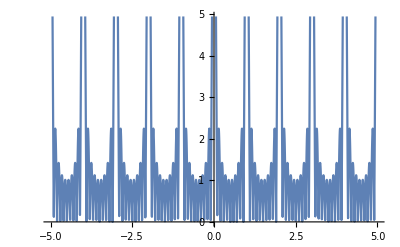

```mathematica
Plot[Abs[A[10,s]],{s,-5,5}]
```

## Chaîne hiérarchique

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
Clear[t];
t[i_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

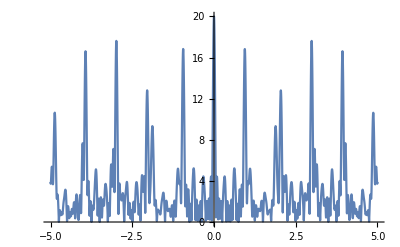

```mathematica
Plot[Abs[A[20,s]/.{v->1.,r->.3}],{s,-5,5},PlotRange->All]
```